```mathematica
Quit[]
```

NFW OF LMC. Density profiles and compute D-factors (without cheese-mask. Just to have an approximate value).
 https://www.aanda.org/articles/aa/pdf/2024/12/aa51578-24.pdf also contains the coordinates of the LMC (dynamical) center

```mathematica
SolarMass=1.988 10^(30);(*Kg*)
eVtoKg=1.782662×10^(-36) ;(*Kg*)
pc=3.0857 10^(16) ;(*in m*)
(*NFW from MR paper https://arxiv.org/pdf/2106.08025*)
rs=9.8;(*kpc*)
ρs=5.1 10^6  SolarMass 1/eVtoKg 10^(-9) (10^3 pc 10^2)^(-3) (*GeV cm-3*)
NFW[r_]:=ρs rs/r (1+r/rs)^(-2);
(*NFW from https://www.aanda.org/articles/aa/pdf/2024/12/aa51578-24.pdf
I use second column from Table1
*)
rs2=10^(4.30) 10^(-3);(*kpc*)
ρs2=10^(-2.47) 10^9 SolarMass 1/eVtoKg 10^(-9) (10^3 pc 10^2)^(-3); (*GeV cm-3*)
NFW2[r_]:=ρs2 rs2/r (1+r/rs2)^(-2);
(*NFW from https://www.aanda.org/articles/aa/pdf/2024/12/aa51578-24.pdf
I use first column from Table1
*)
rs3=10^(4.02) 10^(-3);(*kpc*)
ρs3=10^(-1.99) 10^9 SolarMass 1/eVtoKg 10^(-9) (10^3 pc 10^2)^(-3); (*GeV cm-3*)
NFW3[r_]:=ρs3 rs3/r (1+r/rs3)^(-2);
(*From https://arxiv.org/pdf/2509.13540
From Fig.1: profile valid up to 4-5 kpc, which corresponds to 4.5 -5.7 deg from the center.
*)
(*
The center of LMC they take is l=79.5◦,b=−32.9◦
which should be ...
*)
αE=0.277;
rE=5.65;
ρE=9.36 10^6SolarMass 1/eVtoKg 10^(-9) (10^3 pc 10^2)^(-3) (*GeV cm-3*);
Einasto[r_]:=ρE Exp[-2/αE ((r/rE)^αE-1)]
NFW[50]
```

0.193578

0.00101897

```mathematica
NFW[50]
NFW2[50]
rs2
```

0.00101897

0.0041755

19.9526

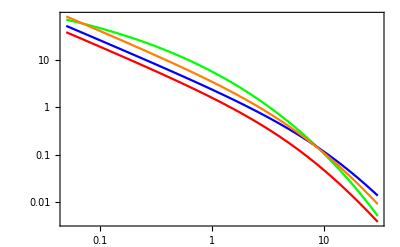

```mathematica
LogLogPlot[{Einasto[r],NFW[r],NFW2[r],NFW3[r]},{r,0.05,30},Frame->True,PlotStyle->{Green,Red,Blue,Orange}]
```

```mathematica
(*Integral until R200 to check that I obtain M200 in Table 1 of https://www.aanda.org/articles/aa/pdf/2024/12/aa51578-24.pdf*)
```

```mathematica
NIntegrate[4 Pi r^2NFW2[r],{r,0,156}] (SolarMass 1/eVtoKg 10^(-9) (10^3 pc 10^2)^(-3))^(-1)
NIntegrate[4 Pi r^2NFW3[r],{r,0,75}] (SolarMass 1/eVtoKg 10^(-9) (10^3 pc 10^2)^(-3))^(-1)
```

4.364×10^11

1.80427×10^11

```mathematica
pc=3.0857 10^(16) ;(*in m*)
Kpc=10^3 pc;(*pc*)
d=50.;(*kpc*)
Profile[r_]:=NFW[r]
RGCθ[s_,θ_]:=Module[{x,y,z},z=s Sin[θ];y=0;x=d-s Cos[θ];Sqrt[x^2+y^2+z^2]]
step=1.;
LosDθ[θ_]:=(Kpc 10^2)(NIntegrate[Profile[RGCθ[s,θ]],{s,0.,d-step}]+NIntegrate[Profile[RGCθ[s,θ]],{s,d-step,d+step},Method->{Automatic,"SymbolicProcessing" -> 0}]+NIntegrate[Profile[RGCθ[s,θ]],{s,d+step,1.5d}])
```

InterpolatingFunction[…]

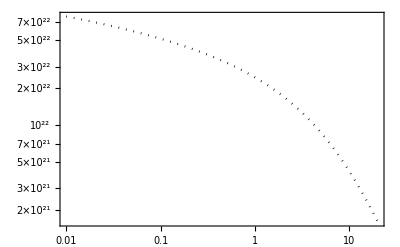

```mathematica
Npoints=300;
θmin=0.01;
θmax=20.;
Do[aθ[i]=10^(Log10[θmin]+Log10[θmax/θmin]*i/Npoints) Pi/180;(*rad*)
aIntelosθ[i]=LosDθ[aθ[i]],{i,0,Npoints}]
dDdΩθLogLog=Interpolation[Table[{Log10@aθ[i],Log10@aIntelosθ[i]},{i,0,Npoints}],InterpolationOrder->1]
dDdΩ[x_]:=10^(dDdΩθLogLog[Log10[x]])
dDdΩ[x_]:=10.^(dDdΩθLogLog[Log10[x]])
LogLogPlot[{dDdΩ[α Pi/180]},{α,θmin ,θmax},Frame->True,PlotStyle->{Darker[Green],{Black,Dotted}}(*,FrameLabel->{StyleFrameLabel["θ [rad]"],StyleFrameLabel["dD/dΩ(α) [GeV cm^-2sr^-1]"]},
FrameStyle-> StyleFrameTicks*)
]
```

```mathematica
50. Tan[3 Pi/180.]
50. Tan[5 Pi/180.]
50. Tan[6 Pi/180.]
```

2.62039

4.37443

5.25521

```mathematica
(*Print[3 Pi/180.," ",dDdΩ[3 Pi/180]]
Print[6 Pi/180.," ",dDdΩ[6 Pi/180]]
Print[10Pi/180.," ",dDdΩ[10 Pi/180]]*)
```

```mathematica
(*2401.16747 Fig.3. They say that they have used NFW. I try to understand what they have taken.*)
3. 10^3 pc 10^2
% 164.46 (Pi/180)^2
```

9.2571×10^21

4.63756×10^20

```mathematica
old=1.57511 10^20;
new=6.35722 10^20;
new/old
```

4.03605

```mathematica
Sqrt[25/9.]
```

1.66667

```mathematica
αint=5.0;
ΔΩ=2Pi(1-Cos[αint Pi/180]);
Dfact=2Pi NIntegrate[Sin[α]dDdΩ[α ],{α, θmin Pi/180., αint Pi/180}];
Print["D GeV cm-2 ",Dfact," for θ [deg] ",αint," D/ΔΩ GeV cm-2 sr-1 ",Dfact/ΔΩ]
```

D GeV cm-2 3.17419×10^20 for θ [deg] 5. D/ΔΩ GeV cm-2 sr-1 1.32759×10^22

```mathematica
(*NFW*)
```

D GeV cm-2 3.17419×10^20 for θ [deg] 5. D/ΔΩ GeV cm-2 sr-1 1.32759×10^22

```mathematica
(*NFW2*)
```

D GeV cm-2 8.26177×10^20 for θ [deg] 6. D/ΔΩ GeV cm-2 sr-1 2.40029×10^22

```mathematica
(*NFW*)
```

D GeV cm-2 4.00704×10^20 for θ [deg] 6. D/ΔΩ GeV cm-2 sr-1 1.16416×10^22

```mathematica
(*NFW*)
```

D GeV cm-2 7.28479×10^20 for θ [deg] 10. D/ΔΩ GeV cm-2 sr-1 7.63159×10^21

```mathematica
(*NFW2*)
```

D GeV cm-2 1.64505×10^21 for θ [deg] 10. D/ΔΩ GeV cm-2 sr-1 1.72336×10^22

```mathematica
(*NFW2*)
```

D GeV cm-2 6.35722×10^20 for θ [deg] 5. D/ΔΩ GeV cm-2 sr-1 2.65888×10^22

```mathematica
(*NFW3*)
```

D GeV cm-2 3.51224×10^20 for θ [deg] 3.

```mathematica
(*NFW2*)
```

D GeV cm-2 2.93981×10^20 for θ [deg] 3. D/ΔΩ GeV cm-2 sr-1 3.41406×10^22

```mathematica
(*Einasto*)
```

D GeV cm-2 4.69476×10^20 for θ [deg] 3.

```mathematica
(*NFW*)
```

D GeV cm-2 1.57511×10^20 for θ [deg] 3. D/ΔΩ GeV cm-2 sr-1 1.82921×10^22

```mathematica
(*NFW*)
```

D GeV cm-2 5.55238×10^19 for θ [deg] 1.5

```mathematica
(*3deg NFW2/NFW*) 
2.93981/1.57511
(*5deg NFW2/NFW*) 
6.35722/3.17418
(*6deg NFW2/NFW*) 
8.26177/4.00704
```

1.86642

2.00279

2.06181

compute D-factors from the MW halo at LMC position

```mathematica
(*(*RA/DEC of https://en.wikipedia.org/wiki/Large_Magellanic_Cloud.
NOT dynamical center.*)
(*05:23:34*)
(5+23/60+34/3600)360/24.
(*-69:45:22*)
-(69 +45./60+22/3600)*)
```

```mathematica
(*RA DEC of dynamical center, second column of of https://www.aanda.org/articles/aa/pdf/2024/12/aa51578-24.pdf.
First transform in H,m,s RA and deg,min,sec DEC*)
80.26
(5+21/60+2.41/3600)360/24.;
−69.26
(*-(4+37/60+2.34/3600)360/24.*)
-(69. +15/60+36/3600.)
(*Input in https://ned.ipac.caltech.edu/forms/calculator.html
5:21:2.41
69:15:36
Output:Galactic
279.88437784 -33.23695025 259.813285
*)
```

80.26

-69.26

-69.26

NFW OF MW

```mathematica
(*NFW from Cirelli-Strumia-Zupan*)
rs=14.46;(*kpc*)
ρs=0.566;(*GeV cm-3*)
Rsun=8.33;(*kpc*)
NFW[r_]:=ρs rs/r (1+r/rs)^(-2)
Profile[r_]:=NFW[r]
RGC[s_,l_,b_]:=Module[{x,y,z},z=s Sin[b];y=s Cos[b]Sin[l];x=Rsun-s Cos[b]Cos[l];Sqrt[x^2+y^2+z^2]]
RGCθ[s_,θ_]:=Module[{x,y,z},z=s Sin[θ];y=0;x=Rsun-s Cos[θ];Sqrt[x^2+y^2+z^2]]
pc=3.0857 10^(16) ;(*in m*)
Kpc=10^3 pc;(*pc*)
step=0.5;
(*Output in GeV cm-2*)
LosD[l_,b_]:=(Kpc 10^2)(NIntegrate[Profile[RGC[s,l,b]],{s,0.,Rsun-step}]+NIntegrate[Profile[RGC[s,l,b]],{s,Rsun-step,Rsun+step},Method->{Automatic,"SymbolicProcessing" -> 0}]+NIntegrate[Profile[RGC[s,l,b]],{s,Rsun,1.5Rsun}])
LosDθ[θ_]:=(Kpc 10^2)(NIntegrate[Profile[RGCθ[s,θ]],{s,0.,Rsun-0.1}]+NIntegrate[Profile[RGCθ[s,θ]],{s,Rsun-0.1, Rsun+0.1}]+NIntegrate[Profile[RGCθ[s,θ]],{s,Rsun+0.1,10 Rsun}])
```

```mathematica
(*(*From SPHEREX notebook as a check*)
lNGC=96.38 Pi/180;
bNGC=29.81 Pi/180;
lmin=lNGC-5.4Pi/180;
lmax=lNGC+5.4Pi/180;
bmin=bNGC-5.4Pi/180;
bmax=bNGC+5.4Pi/180;
ΔΩ=(lmax-lmin)(Sin[bmax]-Sin[bmin]);
Print["ΔΩ in deg2 ",ΔΩ (180/Pi)^2]
Print["dD/dΩ GeV cm-2 sr-1 ",LosDθ[Sqrt[lNGC^2+bNGC^2]]]
Dfact=LosDθ[Sqrt[lNGC^2+bNGC^2]] ΔΩ;
Print["D GeV cm-2 ",Dfact]
Dfact=LosD[lNGC,bNGC] ΔΩ;
Print["D GeV cm-2 ",Dfact]*)
```

```mathematica
(*lLMC=280.4652 Pi/180;
bLMC=-32.8884 Pi/180;
αint=1.5;
ΔΩ=2Pi (1-Cos[αint Pi/180.]);
Print["ΔΩ in deg2 ",ΔΩ (180/Pi)^2]
Print["dD/dΩ GeV cm-2 sr-1 ",LosDθ[Sqrt[lLMC^2+bLMC^2]]]
Dfact=LosDθ[Sqrt[lLMC^2+bLMC^2]] ΔΩ;
Print["D GeV cm-2 ",Dfact," for α [deg] ",αint]
Dfact=LosD[lNGC,bNGC] ΔΩ;
Print["D GeV cm-2 ",Dfact," for α [deg] ",αint]*)
```

Finally compute dD/dΩ. Just for reference, in the Spherex paper for the north patch I had (see TestSpherex.nb):
dDdΩMWNP = 4.34977  10^20/(100 (Pi/180)^2)(*GeV cm-2 sr-1*) =1.4e22

```mathematica
(*Coordinates LMC here https://simbad.u-strasbg.fr/simbad/sim-id?Ident=Large+Magellanic+Cloud*)
lLMC=280.4652 Pi/180;
bLMC=-32.8884 Pi/180;
(*The ones before of dynamical center, small difference*)
lLMC=279.88437784  Pi/180;
bLMC=-33.23695025 Pi/180;

αint=3.0;
ΔΩ=2Pi (1-Cos[αint Pi/180.]);
Print["ΔΩ in deg2 ",ΔΩ (180/Pi)^2]
Print["dD/dΩ GeV cm-2 sr-1 ",LosD[lLMC,bLMC]," ",LosDθ[Sqrt[lLMC^2+bLMC^2]]]
Dfact=LosDθ[Sqrt[lLMC^2+bLMC^2]] ΔΩ;
Print["D GeV cm-2 ",Dfact," for α [deg] ",αint]
Dfact=LosD[lLMC,bLMC] ΔΩ;
Print["D GeV cm-2 ",Dfact," for α [deg] ",αint]
```

ΔΩ in deg2 28.2679

dD/dΩ GeV cm-2 sr-1 1.18027×10^22 1.74785×10^22

D GeV cm-2 1.50506×10^20 for α [deg] 3.

D GeV cm-2 1.01632×10^20 for α [deg] 3.

ΔΩ in deg2 28.2679

dD/dΩ GeV cm-2 sr-1 1.18839×10^22 1.76089×10^22

D GeV cm-2 1.51628×10^20 for α [deg] 3.

D GeV cm-2 1.02331×10^20 for α [deg] 3.

D-factor MW from GC

InterpolatingFunction[…]

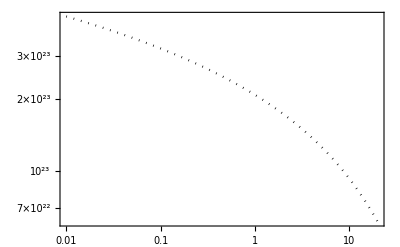

```mathematica
Npoints=300;
θmin=0.01;
θmax=20.;
Do[aθ[i]=10^(Log10[θmin]+Log10[θmax/θmin]*i/Npoints) Pi/180;(*rad*)
aIntelosθ[i]=LosDθ[aθ[i]],{i,0,Npoints}]
dDdΩθLogLog=Interpolation[Table[{Log10@aθ[i],Log10@aIntelosθ[i]},{i,0,Npoints}],InterpolationOrder->1]
dDdΩ[x_]:=10^(dDdΩθLogLog[Log10[x]])
dDdΩ[x_]:=10.^(dDdΩθLogLog[Log10[x]])
LogLogPlot[{dDdΩ[α Pi/180]},{α,θmin ,θmax},Frame->True,PlotStyle->{Darker[Green],{Black,Dotted}}(*,FrameLabel->{StyleFrameLabel["θ [rad]"],StyleFrameLabel["dD/dΩ(α) [GeV cm^-2sr^-1]"]},
FrameStyle-> StyleFrameTicks*)
]
```

```mathematica
Rsun
ρsun=Profile[Rsun]
```

8.33

0.395537

```mathematica
αint=3.0;
Dfact=2Pi NIntegrate[Sin[α]dDdΩ[α ],{α, θmin Pi/180., αint Pi/180}];
Print["D GeV cm-2 ",Dfact," for θ [deg] ",αint]
(*ΔΩ=2Pi(1-Cos[αint/180.]);*)
(*dDdΩ[αint Pi/180 ]/(Rsun Kpc 100  ρsun) *)
```

D GeV cm-2 3.51224×10^20 for θ [deg] 3.

```mathematica
αint=10.0;
Dfact=2Pi NIntegrate[Sin[α]dDdΩ[α ],{α, θmin Pi/180., αint Pi/180}];
Print["D GeV cm-2 ",Dfact," for θ [deg] ",αint]
```

D GeV cm-2 1.11755×10^22 for θ [deg] 10.

```mathematica
αint=15.0;
Dfact=2Pi NIntegrate[Sin[α]dDdΩ[α ],{α, θmin Pi/180., αint Pi/180}];
Print["D GeV cm-2 ",Dfact," for θ [deg] ",αint]
```

D GeV cm-2 2.08901×10^22 for θ [deg] 15.

```mathematica
αint=20.0;
Dfact=2Pi NIntegrate[Sin[α]dDdΩ[α ],{α, θmin Pi/180., αint Pi/180}];
Print["D GeV cm-2 ",Dfact," for θ [deg] ",αint]
```

D GeV cm-2 3.19051×10^22 for θ [deg] 20.

Sterile Nu Decay rate
Eq.1 of https://arxiv.org/pdf/1911.09120

```mathematica
Quit[]
```

```mathematica
(7.2 10^(29))^(-1)
```

1.38889×10^-30

```mathematica
Solve[1/τ==(7.2 10^(29))^(-1) Sinsq2θ/(10^(-8)) mkeV^5,Sinsq2θ]
```

{{Sinsq2θ→(7.2×10^21)/(mkeV^5 τ)}}

```mathematica
(7.2 10^(21))^(-1)
```

1.38889×10^-22

```mathematica
(*Check consistency with eq. 4.13 of https://arxiv.org/pdf/1602.04816*)
```

```mathematica
Sinsq2θ=10^(-8);
θ=Sqrt[Sinsq2θ/4];
5.5 10^(-22) (θ)^2
(7.2 10^(29))^(-1)
(*eq.10 of https://arxiv.org/pdf/2207.04572*)
1.38 10^(−32) Sinsq2θ/10^(-10)
```

1.375×10^-30

1.38889×10^-30

1.38×10^-30